Some notes on our NCCs. When we relax the analytic solution in the unsaturated region, we end up with NCC=1 in the saturated region, even though our analytical form for H means it is 0.5 there (which is what it is before relaxation). However, a true Heaviside function would have the NCC=1 in the saturated region. Why is this, and how does the IVP “know” to move it to the “right” solution?

First idea is to calculate what value of q-qs gives us NCC=1 numerically.

```mathematica
hev[x_, k_] := (1 + Erf[k x])/2
```

```mathematica
ncc[x_,k_] := hev[x,k] + (x k Exp[-k^2 x^2])/Sqrt[π]
```

Trying to solve for when the NCC reaches 1 will fail because there are an infinite number of solutions:

```mathematica
NSolve[Ncc[x, 10^4] -1 == 0,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→InverseFunction[Ncc,1,2][1.,10000]}}

Next, plot both functions and notice two things: 
1. the ncc is steeper than H itself
2. it has a dip and a peak. Plotting a sequence of these with k shows that the dip/peak always has the same value

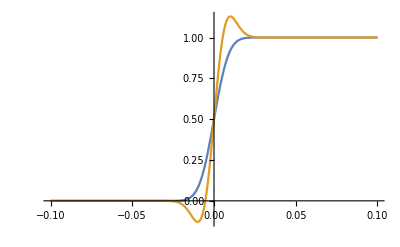

```mathematica
Plot[{hev[x,100],ncc[x,100]}, {x,-0.1,0.1}]
```

General::munfl: Exp[-2499.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-249980.] is too small to represent as a normalized machine number; precision may be lost.

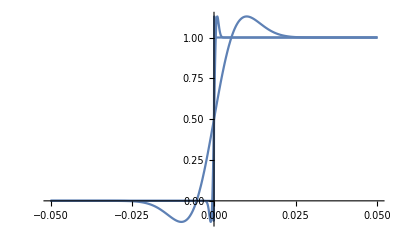

```mathematica
Plot[{Table[ncc[x,10^ks],{ks,Range[2,4]}]}, {x,-0.05,0.05}]
```

Find the minimum and maximum value the NCC takes on:

```mathematica
ans = Solve[D[ncc[x,10^4],x]==0,x]
```

{{x→-1/10000},{x→1/10000}}

```mathematica
minmax = ncc[x,10^4]/.ans
```

{-1/(ⅇ √π)+1/2 (1-Erf[1]),1/(ⅇ √π)+1/2 (1+Erf[1])}

```mathematica
minmax//N
```

{-0.128904,1.1289}